```mathematica
Needs["PlotLegends`"]
```

```mathematica
ClearAll["player*"];
Get[FileNameJoin[{DirectoryName[NotebookFileName[]],"data.txt"}]];
```

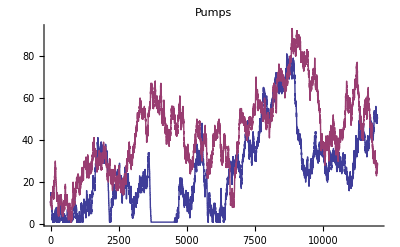

```mathematica
ListPlot[{player1pumps,player2pumps},Joined->True,PlotLegend->{"Player 1", "Player 2"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Pumps"]
```

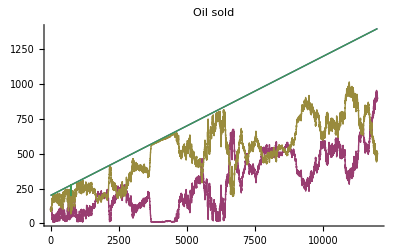

```mathematica
ListPlot[{oildemand,player1sold,player2sold,player1sold+player2sold},Joined->True,PlotLegend->{"Demand", "Player 1", "Player 2", "Total"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Oil sold"]
```

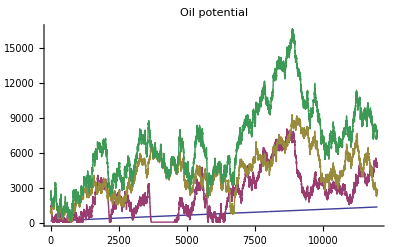

```mathematica
ListPlot[{oildemand,player1potential,player2potential,player1potential+player2potential},Joined->True,PlotLegend->{"Demand", "Player 1", "Player 2", "Total"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Oil potential"]
```

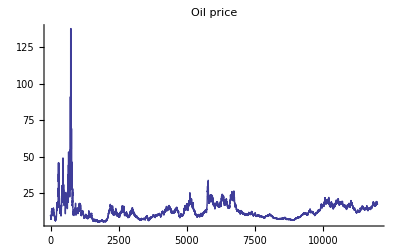

```mathematica
ListPlot[oilprice,Joined->True,PlotLabel->"Oil price"]
```

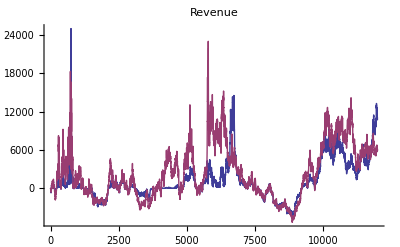

```mathematica
ListPlot[{player1revenue,player2revenue},Joined->True,PlotLabel->"Revenue",PlotLegend->{"Player 1", "Player 2"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

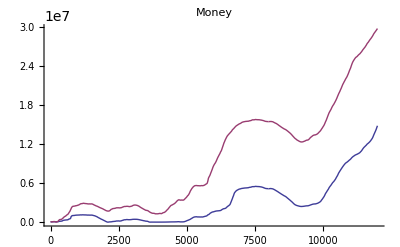

```mathematica
ListPlot[{player1money,player2money},Joined->True,PlotLabel->"Money",PlotLegend->{"Player 1", "Player 2"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```